```mathematica
AppendTo[$Path,"C:\\Users\\Matija\\Desktop\\NRO 2DN"](*!!!Dodamo path v katerem je shranjen naš modul s funkcijo mccpi!!! NUJNO DOLOČITE PATH KJER STE SHRANILI DATOTEKO "MyPackage"!!!*)
```

{C:\Users\Matija\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\12.3\SystemFiles\Links,C:\Users\Matija\AppData\Roaming\Mathematica\Kernel,C:\Users\Matija\AppData\Roaming\Mathematica\Autoload,C:\Users\Matija\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Matija,C:\Program Files\Wolfram Research\Mathematica\12.3\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\12.3\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\12.3\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\12.3\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\12.3\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\12.3\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\12.3\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\12.3\SystemFiles\Data\ICC,C:\Users\Matija\Desktop\NRO 2DN}

```mathematica
Get["MyPackage`"](*Prikličemo naš modul*)
```

```mathematica
seznampij={};(*To je seznam izračunanih števil π*)
seznamnapak = {};(*To je seznam odstopanj izračunanih števil π*)

areapi[it_]:=Module[{i},For[i=1,i<it+1,i++,tocke=mccpi[i];(*Funkcija kliče mccpi z i naključnimi točkami. mccpi nam vrne seznama točk znotraj kroga in znotraj kvardata*)
pij=N[4*Dimensions[tocke[[1]]][[1]]/(Dimensions[tocke[[2]]][[1]]+Dimensions[tocke[[1]]][[1]])];(*Iz števila točk znotraj kroga in kvadrata lahko izračunamo število pi po metodi Monte Carlo in to število pripnemo v seznam vseh izračunanih števil π*)
AppendTo[seznampij,pij];napaka = pij-π;(*Izračunamo še odstopanje izračunanega števila π od dejanskega in to napako pripnemo v seznam z vsemi napakami*)
AppendTo[seznamnapak,napaka]];tockekroga=tocke[[1]];(*Določimo seznam točk znotraj kroga, to bomo uporabili kasneje pri vizualizaciji*)
tockekvadrata=tocke[[2]];
(*Določimo seznam točk znotraj kvadrata, to bomo uporabili kasneje pri vizualizaciji*)StringForm["Seznam rezultirajočih približkov pi je `` odstopanje teh števil od dejanskega je ``.",seznampij,seznamnapak]];
```

```mathematica
areapi[100](*Kličemo funkcijo areapi, v oglate oklepaje vnesemo željeno število iteracij*)
```

Seznam rezultirajočih približkov pi je {4.,4.,2.66667,2.,3.2,2.66667,3.42857,3.5,3.55556,2.8,2.90909,4.,4.,3.14286,3.2,3.,2.58824,3.55556,2.10526,3.4,3.42857,2.90909,3.13043,3.5,3.04,3.07692,2.96296,3.14286,3.58621,2.8,3.48387,3.75,3.75758,2.94118,3.42857,3.11111,2.81081,2.73684,3.38462,3.1,3.21951,3.33333,2.88372,2.72727,3.55556,2.69565,2.89362,3.,2.85714,3.12,2.98039,3.38462,3.32075,3.11111,2.83636,3.28571,2.87719,3.37931,3.32203,3.6,2.81967,3.35484,3.30159,3.5625,2.83077,2.9697,3.40299,3.05882,2.95652,3.31429,3.09859,3.44444,3.06849,3.02703,3.2,3.21053,3.06494,3.48718,2.98734,3.05,3.11111,2.82927,3.37349,3.09524,3.34118,3.2093,2.8046,3.59091,3.10112,3.06667,3.2967,2.82609,3.13978,3.19149,3.24211,3.25,3.34021,2.93878,3.35354,2.96} odstopanje teh števil od dejanskega je ….

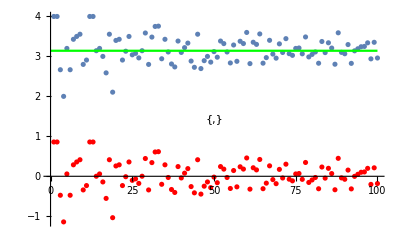

```mathematica
(*Narišemo graf izračunanih števil π za vsako iteracijo, rdeča črta predstavlja dejansko vrednost števila π*)
a=ListPlot[seznampij];
b=ListPlot[seznamnapak,PlotStyle->Red];
c=Plot[π,{x,0,Dimensions[seznampij][[1]]},PlotStyle->Green];
graf=Show[a,b,c,PlotRange->All,AxesLabel->{"Število iteracij"}];
legendedgraf=Legended[graf,Placed[{PointLegend[{Blue,Red},{"Približek π","Odstopanje od π"}],LineLegend[{Green},{"Dejanski π"}]},{0.5,0.5}]];

legendedgraf
```

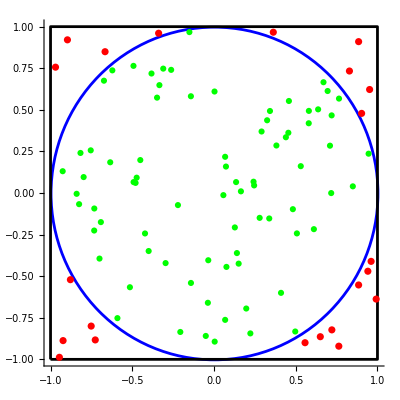

```mathematica
(*Vizualiziramo točke znotraj kroga in znotraj kvadrata*)
krog=Graphics[{Blue,Thickness[0.005],Circle[{0,0},1]}];
kvadrat = Graphics[{EdgeForm[{Thickness[0.005],Black}],FaceForm[Transparent],Rectangle[{-1,-1},{1,1}]}];
notranje =ListPlot[tockekroga,PlotStyle->Green];
zunanje=ListPlot[tockekvadrata,PlotStyle->Red];
Show[krog,kvadrat,notranje,zunanje,Axes->True]
```